```mathematica
SetDirectory[NotebookDirectory[]]
M2=3;
M3=3;
mat1[s_,k_,ω_,As_,ks_,height_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*((-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2))-(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+(k+n*ks)^2*ν2)+(g+σ/ρ*(k+n*ks)^2)*(k+n*ks))*KroneckerDelta[m,o]*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]];
mat2[s_,k_,ω_,As_,ks_,height_]:=ArrayFlatten[Table[Exp[-(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l-1,I*(k+n*ks)*As]-I/2*ks*As*BesselJ[n-l+1,I*(k+n*ks)*As])+Exp[(k+n*ks)*height]/(Exp[k*height]+Exp[-k*height])*(-ω^2*(k+n*ks)/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1])*(BesselJ[n-l,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l-1,-I*(k+n*ks)*As]+I/2*ks*As*BesselJ[n-l+1,-I*(k+n*ks)*As]),{n,-M2,M2},{l,-M2,M2},{m,-M3,M3},{o,-M3,M3}]]
mat3[s_,k_,ω_,height_]:=ArrayFlatten[Table[((-ω^2*(s+m)^2+I*ω*(s+m)*(ν1+k^2*ν2))+Tanh[k*height]*(g+σ/ρ*k^2)*k)*KroneckerDelta[m,o],{m,-M3,M3},{o,-M3,M3}]];
mat4[s_,k_,ω_,height_]:=ArrayFlatten[Table[-Tanh[k*height]*(ω^2*k/2)*(KroneckerDelta[m,o+1]+KroneckerDelta[m,o-1]),{m,-M3,M3},{o,-M3,M3}]]
```

/Users/zack/Documents/oscillators/faraday

```mathematica
ν1=2.0;
ν2=0.1;
g=980;
σ=72;
ρ=1;
```

### Harmonic and subharmonic tongues

{27.2612,Null}

{25.7315,Null}

{66.3946,Null}

{66.7086,Null}

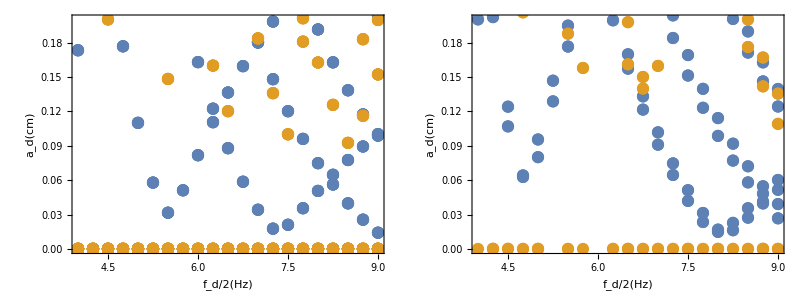

```mathematica
length=12;
ks=(3 π)/2;
ω1=2*Pi*8;
ω2=2*Pi*18;
dω=2*Pi*0.5;
kmin=0;
kmax=ks;
height=0.5;
AbsoluteTiming[Monitor[vals1=Flatten[Table[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,0.0,ks,height],mat2[0.5,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}],1];,1.0*(k-kmin)/(kmax-kmin)];]
AbsoluteTiming[Monitor[vals2=Flatten[Table[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,0.0,ks,height],mat2[0.0,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}],1];,1.0*(k-kmin)/(kmax-kmin)];]
As=0.45;
AbsoluteTiming[Monitor[vals3=Flatten[Table[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,As,ks,height],mat2[0.5,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}],1];,1.0*(k-kmin)/(kmax-kmin)];]
AbsoluteTiming[Monitor[vals4=Flatten[Table[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,As,ks,height],mat2[0.0,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}],1];,1.0*(k-kmin)/(kmax-kmin)];]
p1=ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
p2=ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
Grid[{{p1,p2}}]
```

{327.642,Null}

{348.88,Null}

{335.886,Null}

{317.529,Null}

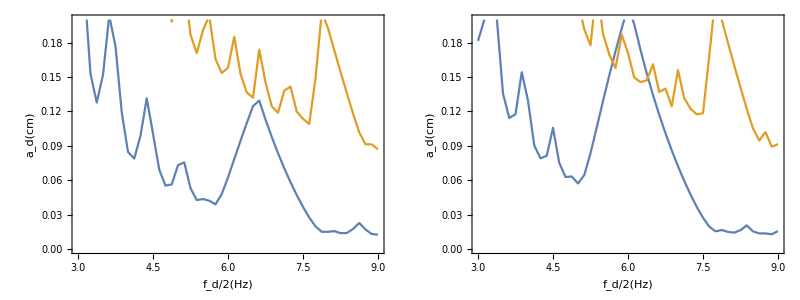

```mathematica
length=24;
ks=(3 π)/2;
ω1=2*Pi*6;
ω2=2*Pi*18;
dω=2*Pi*0.25;
kmin=0;
kmax=ks;
height=0.5;

As=0.4;
AbsoluteTiming[Monitor[vals1=Table[ParallelTable[val=Eigenvalues[{mat1[0.5,k,ω,As,ks,height],mat2[0.5,k,ω,As,ks,height]}];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}];,1.0*(k-kmin)/(kmax-kmin)];]
AbsoluteTiming[Monitor[vals2=Table[ParallelTable[val=Eigenvalues[{mat1[0.0,k,ω,As,ks,height],mat2[0.0,k,ω,As,ks,height]}];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}];,1.0*(k-kmin)/(kmax-kmin)];]

As=0.45;
AbsoluteTiming[Monitor[vals3=Table[ParallelTable[val=Eigenvalues[{mat1[0.5,k,ω,As,ks,height],mat2[0.5,k,ω,As,ks,height]}];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}];,1.0*(k-kmin)/(kmax-kmin)];]
AbsoluteTiming[Monitor[vals4=Table[ParallelTable[val=Eigenvalues[{mat1[0.0,k,ω,As,ks,height],mat2[0.0,k,ω,As,ks,height]}];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{k,kmin,kmax,2*Pi/length}];,1.0*(k-kmin)/(kmax-kmin)];]


freqs=Table[ω/(2*2*Pi),{ω,ω1,ω2,dω}];
p1=ListPlot[{MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals1,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs,MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals2,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
p2=ListPlot[{MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals3,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs,MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals4,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
Grid[{{p1,p2}}]
```

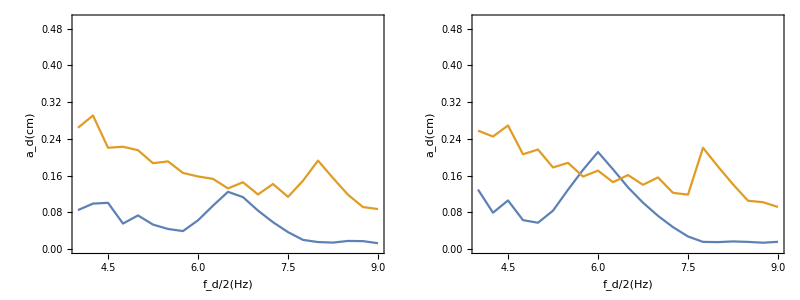

```mathematica
freqs=Table[ω/(2*2*Pi),{ω,ω1,ω2,dω}];
p1=ListPlot[{MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals1,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs,MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals2,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
p2=ListPlot[{MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals3,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs,MinimalBy[Cases[Flatten[Abs[Cases[#,u_/;Abs[Im[u[[2]]]]<10^-4&&Re[u[[2]]]>10^-2]]&/@#&/@vals4,2],u_/;u[[1]]==#],#[[2]]&][[1]]&/@freqs},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
Grid[{{p1,p2}}]
```

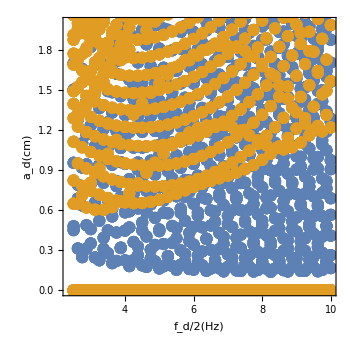

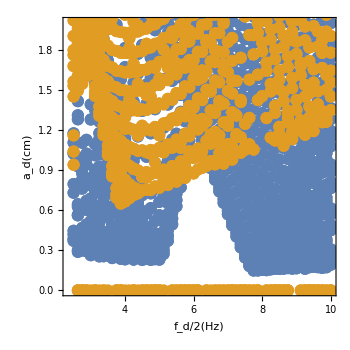

```mathematica
vals1=Partition[Flatten[Import["data/harmonic1.dat"]],2];
vals2=Partition[Flatten[Import["data/harmonic2.dat"]],2];
vals3=Partition[Flatten[Import["data/harmonic3.dat"]],2];
vals4=Partition[Flatten[Import["data/harmonic4.dat"]],2];
ListPlot[{{#[[1]],#[[2]]*(4*Pi*#[[1]])^2/980}&/@vals1,{#[[1]],#[[2]]*(4*Pi*#[[1]])^2/980}&/@vals2},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{Automatic,{0,2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]

ListPlot[{{#[[1]],#[[2]]*(4*Pi*#[[1]])^2/980}&/@vals3,{#[[1]],#[[2]]*(4*Pi*#[[1]])^2/980}&/@vals4},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[a,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{Automatic,{0,2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
```

```mathematica
Export["data/harmonic1.dat",Flatten[vals1,1]]
Export["data/harmonic2.dat",Flatten[vals2,1]]
Export["data/harmonic3.dat",Flatten[vals3,1]]
Export["data/harmonic4.dat",Flatten[vals4,1]]
```

data/harmonic1.dat

data/harmonic2.dat

data/harmonic3.dat

data/harmonic4.dat

Part::partd: Part specification 2.5⟦1⟧ is longer than depth of object.

Part::partd: Part specification 2.5⟦2⟧ is longer than depth of object.

Part::partd: Part specification 2.5⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

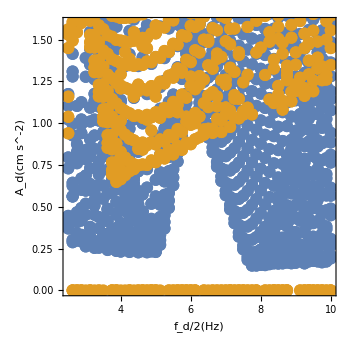

```mathematica
ListPlot[{{#[[1]],#[[2]]*(4*Pi*#[[1]])^2/980}&/@Flatten[vals3,1],{#[[1]],#[[2]]*(4*Pi*#[[1]])^2/980}&/@Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm s^-2)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(2*2*Pi),ω2/(2*2*Pi)},{0,1.6}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
```

```mathematica
2*(ks/2*Tanh[ks/2*height]*(g+σ/ρ*(ks/2)^2))^(1/2)/(2*Pi)
2*((ks/2-2*Pi/length)*Tanh[(ks/2-2*Pi/length)*height]*(g+σ/ρ*(ks/2-2*Pi/length)^2))^(1/2)/(2*Pi)
```

16.5031

12.8173

```mathematica
height=0.1;
(ks/2*Tanh[ks/2*height]*(g+σ/ρ*(ks/2)^2))^(1/2)/(2*Pi*2)
(ks*Tanh[ks*height]*(g+σ/ρ*(ks)^2))^(1/2)/(2*Pi*2)
```

2.18238

5.81376

```mathematica
ω1=2*Pi*2;
ω2=2*Pi*18;
dω=2*Pi*0.1;
kmin=0;
kmax=2*Pi/length*16;
height=0.1;
AbsoluteTiming[vals1=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,0.0,ks,height],mat2[0.5,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
AbsoluteTiming[vals2=Flatten[DeleteCases[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,0.0,ks,height],mat2[0.0,k,ω,0.0,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],{}],1];]
As=0.9*height;
AbsoluteTiming[vals3=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.5,k,ω,As,ks,height],mat2[0.5,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
AbsoluteTiming[vals4=DeleteCases[Flatten[ParallelTable[val=Abs[Cases[Eigenvalues[{mat1[0.0,k,ω,As,ks,height],mat2[0.0,k,ω,As,ks,height]}],u_/;Abs[Im[u]]<10^-4]];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω},{k,kmin,kmax,2*Pi/length}],1],{}];]
p1=ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
p2=ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,2}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350];
Grid[{{p1,p2}}]
```

{224.486,Null}

{210.659,Null}

{556.611,Null}

### Compare with finite elements

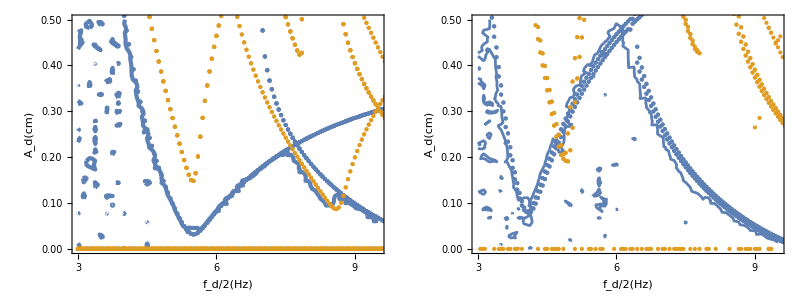

```mathematica
filebases={"sweeps/sharpamp/1001"};
cols={ColorData[97,"ColorList"][[1]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p1=Show[Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[3]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}],ListPlot[{Flatten[vals1,1],Flatten[vals2,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.5}},PlotStyle->Directive[PointSize[0.01]],ImageSize->350]];
filebases={"sweeps/sharpamp/1003"};
cols={ColorData[97,"ColorList"][[1]]};
sweeps=Flatten[Table[If[FileExistsQ[#<>"/params"<>ToString[i]<>".txt"],Internal`StringToDouble/@#&/@DeleteCases[StringSplit/@StringSplit[Import[#<>"/params"<>ToString[i]<>".txt"],"\n"],{}],{}],{i,1,100}],1]&/@filebases;
p2=Show[Show@@Table[ListContourPlot[{#[[1]]/2,#[[2]]/(2*Pi*#[[1]])^2*980,#[[3]]}&/@sweeps[[i,All,{1,2,4}]],Contours->{0.0},PlotRange->{{3,9.5},{0,0.5}},ContourShading->None,ContourStyle->{Directive[cols[[i]],Opacity[1],AbsoluteThickness[2]]},LabelStyle->Directive[16,Black], FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},FrameStyle->Directive[Black,AbsoluteThickness[2.0]],ImageSize->300,ImagePadding->{{65,10},{65,10}},FrameTicks->{{Table[{i,PaddedForm[i,{2,2}]},{i,0,0.5,0.1}],Table[{i,""},{i,0,0.5,0.1}]},{Table[{i,i},{i,3,16,3}],Table[{i,""},{i,3,16,3}]}}],{i,1,Length[sweeps]}],ListPlot[{Flatten[vals3,1],Flatten[vals4,1]},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->False,PlotRange->{{ω1/(4*Pi),ω2/(4*Pi)},{0,0.5}},PlotStyle->Directive[PointSize[0.01]],ImageSize->350]];
Grid[{{p1,p2}}]
```

```mathematica
gap=2*Pi/length*3/2;
ks=2*gap;
height=0.5;
As=0.9*height;
dϵ=0.01;
ω=0.8*2*(gap*Tanh[height*gap]*(g+σ/ρ*gap^2))^(1/2);
ω/(2*Pi*2)
```

6.60123

### Frequency ratio sweep

```mathematica
ν1=0.5;
ν2=0.0;
g=980;
σ=72;
ρ=1;
length=4.0;
gap=2*Pi/length*3/2;
ks=2*gap;
height=0.45;
As=0.4;
kmin=0;
kmax=ks;
k=2*Pi/length;
ω=2*Pi*27;
```

```mathematica
(* What value of k lies close to subcritical resonance with this omega?? *)
```

{292.425,Null}

{129.927,Null}

{{0.499,9.98491×10^-7,-0.0593267}}

{{0.4988,-9.6976×10^-7,0.112079}}

0.0593267

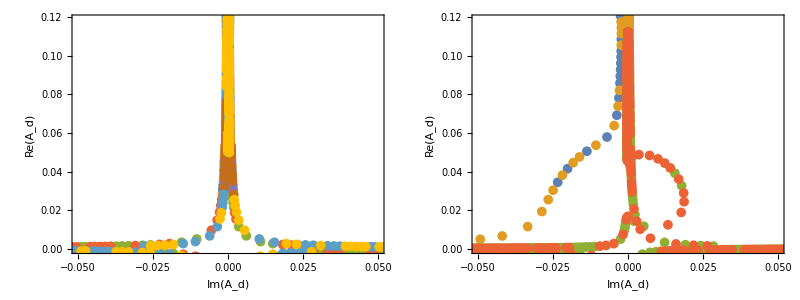

```mathematica
M2=3;
M3=3;
dϵ=2*10^-4;
ν1=0.05;
ϵmin=0.1;
ϵmax=0.2;
dϵ=
AbsoluteTiming[vals3=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,ϵmin,ϵmax,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}]];]
AbsoluteTiming[vals4=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,ϵmin,ϵmax,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,-0.05,0.05,2*10^-4}]];]

crit=MinimalBy[Cases[Flatten[vals4[[All,All,All]],1],u_/;Abs[u[[2]]]<10^-6],Abs[#[[3]]]&]
MinimalBy[Cases[Flatten[vals3[[All,All,All]],1],u_/;Abs[u[[2]]]<10^-6],Abs[#[[3]]]&]
scale=Abs[crit[[1,3]]]
Grid[{{ListPlot[Join[Transpose[vals4[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals4[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1],ListPlot[Join[Transpose[vals3[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals3[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]}}]
```

{223.101,Null}

{91.4665,Null}

{{0.5,1.39587×10^-12,-0.0593388}}

0.0593388

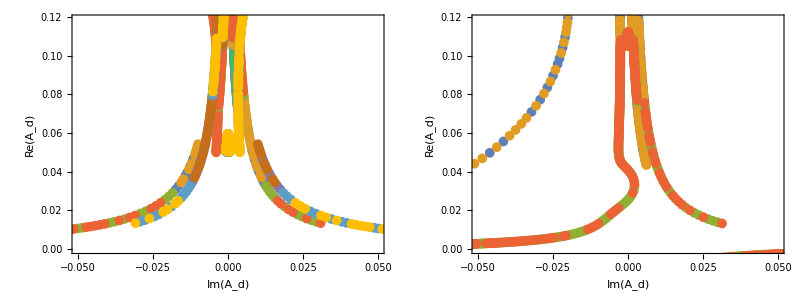

```mathematica
M2=3;
M3=3;
dϵ=2*10^-4;
ω=2*Pi*27;
ν1=0.5;
AbsoluteTiming[vals3=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.1,0.2,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}]];]
AbsoluteTiming[vals4=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.1,0.2,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,-0.05,0.05,2*10^-4}]];]

crit=MinimalBy[Cases[Flatten[vals4[[All,All,All]],1],u_/;Abs[u[[2]]]<10^-6],Abs[#[[3]]]&]
scale=Abs[crit[[1,3]]]
Grid[{{ListPlot[Join[Transpose[vals4[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals4[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1],ListPlot[Join[Transpose[vals3[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals3[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]}}]
```

```mathematica
(* The subharmonic mode dominates at smaller driving amplitude.  Can we put the driving frequency in a band gap so that this is larger? *)
```

{232.712,Null}

{94.5471,Null}

{{0.5,-1.53112×10^-13,0.0310914}}

0.0310914

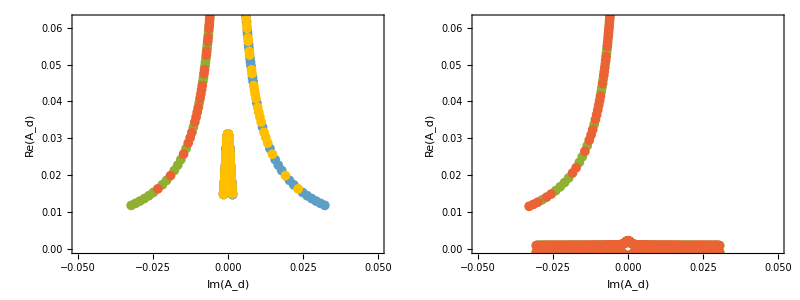

```mathematica
M2=3;
M3=3;
dϵ=2*10^-4;
ω=2*Pi*27;
ν1=0.5;
k=0.5340707511102647;
AbsoluteTiming[vals3=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.1,0.2,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}]];]
AbsoluteTiming[vals4=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.1,0.2,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,-0.05,0.05,2*10^-4}]];]

crit=MinimalBy[Cases[Flatten[vals4[[All,All,All]],1],u_/;Abs[u[[2]]]<10^-6],Abs[#[[3]]]&]
scale=Abs[crit[[1,3]]]
Grid[{{ListPlot[Join[Transpose[vals4[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals4[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1],ListPlot[Join[Transpose[vals3[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals3[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]}}]
```

```mathematica
(*For larger damping, the anharmonic excitations never become unstable. *)
```

```mathematica
M2=3;
M3=3;
dϵ=2*10^-4;
ω=2*Pi*27;
ν1=1.0;
AbsoluteTiming[vals3=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.1,0.2,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,As,ks,height],mat2[ϵ,k,ω,As,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}]];]
AbsoluteTiming[vals4=Join[ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.1,0.2,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,0.45,0.55,2*10^-4}],ParallelTable[val=Eigenvalues[{mat1[ϵ,k,ω,0,ks,height],mat2[ϵ,k,ω,0,ks,height]}];{ϵ,Im[#],Re[#]}&/@val,{ϵ,-0.05,0.05,2*10^-4}]];]

crit=MinimalBy[Cases[Flatten[vals4[[All,All,All]],1],u_/;Abs[u[[2]]]<10^-6],Abs[#[[3]]]&]
scale=Abs[crit[[1,3]]]
Grid[{{ListPlot[Join[Transpose[vals4[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals4[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1],ListPlot[Join[Transpose[vals3[[All,All,{2,3}]]],Transpose[{-#[[1]],#[[2]]}&/@#&/@vals3[[All,All,{2,3}]]]],Joined->False,PlotRange->{{-0.05,0.05},{0,2*scale}},PlotStyle->Directive[PointSize[0.02]],ImageSize->350,Axes->False,Frame->True,FrameLabel->{Im[Subscript[A,d]],Re[Subscript[A,d]]},LabelStyle->Directive[16,Black],FrameStyle->Directive[Black,AbsoluteThickness[2]],AspectRatio->1]}}]
```

{233.775,Null}

{90.73,Null}

{{0.5,2.79773×10^-12,-0.0593652}}

0.0593652

-Graphics-

### Plots

```mathematica
dω=2*Pi*0.05;
AbsoluteTiming[vals5=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat1[0.0,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];val2=Abs[Cases[Eigenvalues[{mat1[0.5,2*Pi/length,ω,0.4,ks],mat2[0.0,2*Pi/length,ω,0.4,ks]}],u_/;Abs[Im[u]]<10^-2]];
val=Join[val1,val2];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
AbsoluteTiming[vals1=DeleteCases[ParallelTable[val1=Abs[Cases[Eigenvalues[{mat3[0.5,2*Pi/length,ω],mat4[0.5,2*Pi/length,ω]}],u_/;Abs[Im[u]]<10^-6]];
val2=Abs[Cases[Eigenvalues[{mat3[0.5,2*Pi/length*2,ω],mat4[0.5,2*Pi/length*2,ω]}],u_/;Abs[Im[u]]<10^-6]];val3=Abs[Cases[Eigenvalues[{mat3[0.0,2*Pi/length*3,ω],mat4[0.0,2*Pi/length*3,ω]}],u_/;Abs[Im[u]]<10^-6]];
val=Join[val1,val2,val3];If[Length[val]>0,Transpose[{ConstantArray[ω/(2*2*Pi),Length[val]],val}],{}],{ω,ω1,ω2,dω}],{}];]
```

{16.6074,Null}

{0.093006,Null}

```mathematica
ListPlot[{First@MinimalBy[#,#[[2]]&]&/@vals1,First@MinimalBy[#,#[[2]]&]&/@vals5},Axes->False,Frame->True,AspectRatio->1,FrameLabel->{{DisplayForm[RowBox[{HoldForm[Subscript[A,d]],"(cm)"}]],None},{DisplayForm[RowBox[{Subscript[f,d],"/",2,"(Hz)"}]],None}},LabelStyle->Directive[Black,16],FrameStyle->Directive[Black,AbsoluteThickness[2]],Joined->True,PlotRange->{{3,9.5},{0,0.5}},PlotStyle->Directive[PointSize[0.025]],ImageSize->350]
Export["data/flatfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals1,"Table"]
Export["data/periodicfloquet.txt",First@MinimalBy[#,#[[2]]&]&/@vals5,"Table"]
```

-Graphics-

data/flatfloquet.txt

data/periodicfloquet.txt